```mathematica
<<Taggar`MGroups`
```

```mathematica
Subscript[S, 5]=MPermutationsGroup[5]
```

```mathematica
raw=MSubgroups[Subscript[S, 5],MPresentation->"Raw"];
```

```mathematica
cvt[{x_,y_}]:={x,Style["⟨"<>StringRiffle[y,","]<>"⟩",White]}
```

```mathematica
subs=raw[[All,1]];
map=Association@Thread[Rule@@@(cvt/@raw)];
```

```mathematica
rules=Select[Tuples[subs,2],SubsetQ[#[[2]],#[[1]]]&];
edges=EdgeList@TransitiveReductionGraph[Rule@@@rules]
```

```mathematica
?FindPath
```

```mathematica
paths=FindPath[g,{"(1)"},Sort@MGroupDomain[Subscript[S, 5]],Infinity,All]
```

```mathematica
g=Graph[edges,GraphLayout->"RadialEmbedding",VertexSize->1.25,VertexStyle->RGBColor["#D5D2D2"],EdgeShapeFunction->"Line",EdgeStyle->{Thin,Lighter[RGBColor["#232326"],0.2]},Background->None]
```

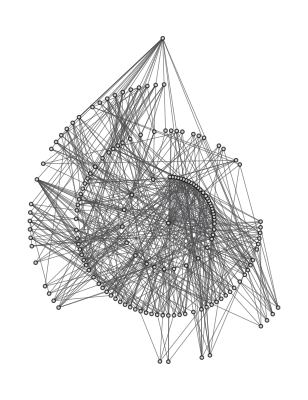

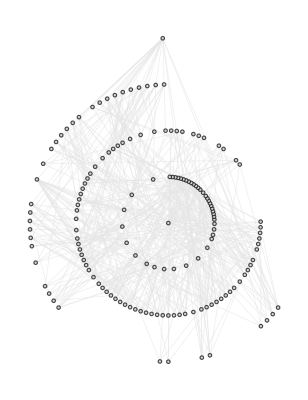

```mathematica
g=-Graphics-;
```

```mathematica
spaths=RandomSample[paths,6];
```

```mathematica
ani=Table[
p=spaths[[i]];
labels=Thread[p->(map/@p)];
lgh=(Style[#,{RGBColor["#FF80FA"],Thick}]&@*Rule)@@@Partition[p,2,1];
pg=PathGraph[p,VertexStyle->RGBColor["#FF80FA"]];
HighlightGraph[g,{pg,lgh},VertexLabels->labels,EdgeStyle->RGBColor["#FF80FA"],PlotRange->All,Background->None],
{i,1,Length@spaths,1}
]
```

```mathematica
Do[
Export[NotebookDirectory[]<>"../s5/s5g"<>ToString[i]<>".svg",ani[[i]],Background->None],
{i,Length@ani}
]
```

```mathematica
PlotRange
```